{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

SetOptions::optnf: Joined is not a known option for Plot.

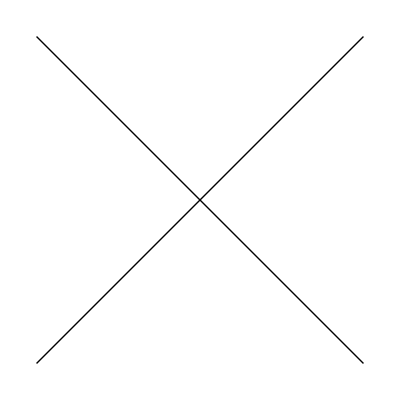
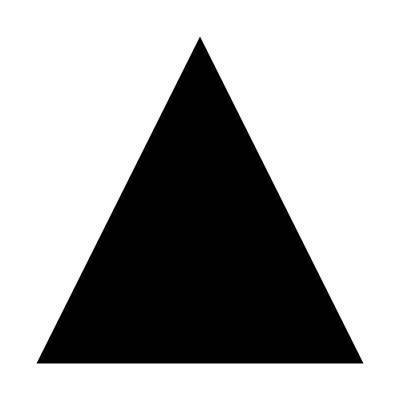
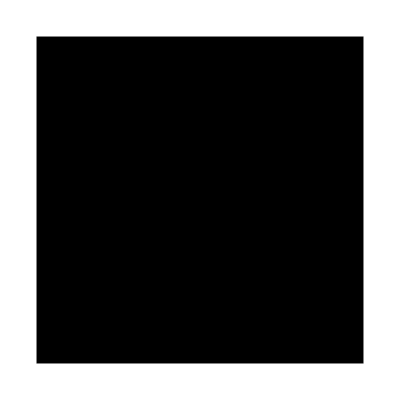
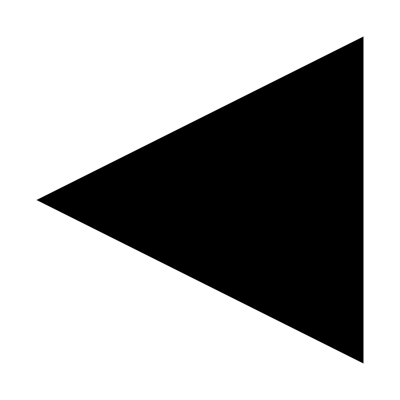
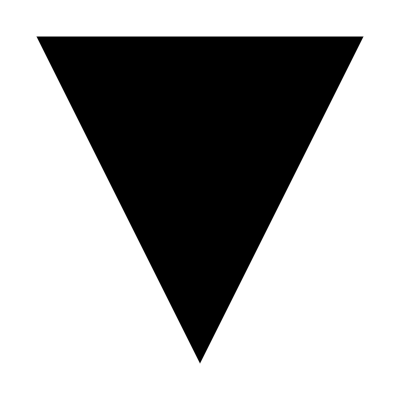
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage[rgb,dvipsnames]{xcolor},\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373},\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392},\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882},\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→10,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
<<MaTeX`
<<PolygonPlotMarkers`

myblue=RGBColor[0.2745098039,0.5333333333,0.9450980392];
myred=RGBColor[0.9176470588,0.2588235294,0.2078431373];
mygreen=RGBColor[0.2039215686,0.662745098,0.3176470588];
myyellow=RGBColor[0.9764705882,0.7333333333,0.1764705882];
mygray=RGBColor[109/255//N,109/255//N,109/255//N];
mylightgray=RGBColor[185/255//N,185/255//N,185/255//N];
thickness=0.002;
size=0.05;
font="Latin Modern Roman";
imagSize=200;
fontSize=10;
markersize=0.025;
cm=72/2.54;

ts=0.02*{1,1/GoldenRatio};

fm[name_,size_:4]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes

fm[name_,size_:5]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

fm2[name_,size_:3]:=Graphics[{EdgeForm[],PolygonMarker[name,Offset[size]]},AlignmentPoint->{0,0}];

GetScaledLogTicks[min_,max_,scale_]:=Module[{ticks},ticks=#[Log[min],Log[max]]&/@{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]};
(*scale the tick length*)Table[{Exp[#[[1]]],#[[2]],scale*#[[3]]}&/@ticks[[i]],{i,2}]]

SetOptions[MaTeX,FontSize->fontSize]

SetOptions[ListPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[Plot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black,Directive[Black,AbsoluteThickness[0.5]]],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

SetOptions[ListLogLogPlot,FrameStyle->Directive[FontFamily->font,FontSize->fontSize,FontColor->Black],Frame->True,Axes->False,FrameTicksStyle->Black,Joined->True,PlotMarkers->Automatic];

align = Sequence[AlignmentPoint -> {0, 0}, AxesOrigin -> {0, 0}, BaselinePosition -> Axis];
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
plotRangePadding = .01;
edgeThickness = .1;
size = Sequence[PlotRange -> {{-2, 2}, {-2, 2}}, PlotRangePadding -> Scaled[edgeThickness/2 + plotRangePadding], ImagePadding -> 0, ImageMargins -> 0];
halfTr = {Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Line[{{-1, -1}, {1, 1}}], Line[{{-1, 1}, {1, -1}}](*EdgeForm[],FaceForm[Opacity[1]],Polygon[{{0,2},{2/Sqrt[3],0},{-(2/Sqrt[3]),0}}],EdgeForm[{Opacity[1],Thickness[edgeThickness],JoinForm["Round"]}],FaceForm[],Polygon[{{0,2},{Sqrt[3],-1},{-Sqrt[3],-1}}]*)}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Polygon[{{0, 1}, {1, -1}, {-1, -1}}]}, align,PlotRangePadding->0,ImagePadding->0],
   Graphics[{EdgeForm[{mygray, AbsoluteThickness[edgeThickness], JoinForm["Round"]}], Rectangle[{-1, -1}, {1, 1}]}, align,PlotRangePadding->0,ImagePadding->0]};
halfTr = Flatten[{halfTr, Table[halfTr /. p : {_?NumericQ, _?NumericQ} :> RotationMatrix[θ].p, {θ, {Pi/2,  Pi}}]}, 2] /. "size" -> size
Magnify[#, .1] & /@ halfTr;
ListPlot[Flatten[Table[{{n, y}}, {y, Range[1, 3]}, {n, 20}], 1], PlotMarkers -> Table[{s, 0.07}, {s, halfTr}], PlotStyle -> ColorData[60, "ColorList"], GridLines -> {Range[20], Range[3]}, PlotRange -> {{0, 21}, {0, 4}}, Axes -> False, Frame -> True];

new={{"GoogleGradient","",{}},{"Gradients"},1,{0,1},{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred},""};
ColorData["GoogleGradient"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];

new={{"GoogleGradientRev","",{}},{"Gradients"},1,{0,1},Reverse[{myblue,Lighter[myblue,.5],Lighter[myblue,.75],White,Lighter[myred,.75],Lighter[myred,.5],myred}],""};
ColorData["GoogleGradientRev"]//Quiet;
AppendTo[DataPaclets`ColorDataDump`colorSchemes,new];
AppendTo[DataPaclets`ColorDataDump`colorSchemeNames,new[[1,1]]];
SetOptions[MaTeX,"Preamble"->{"\\usepackage[rgb,dvipsnames]{xcolor}","\\definecolor{myred}{rgb}{0.9176470588, 0.2588235294, 0.2078431373}","\\definecolor{myblue}{rgb}{0.2745098039, 0.5333333333, 0.9450980392}","\\definecolor{myyellow}{rgb}{0.9764705882, 0.7333333333, 0.1764705882}","\\definecolor{mygreen}{rgb}{0.2039215686, 0.662745098, 0.3176470588}"}]
```

```mathematica
Manipulate[Plot[Exp[-(x/σ)^2],{x,0,10}],{σ,0.001,1}]
```

```mathematica
f[Λ_,r_,s_]:=NIntegrate[BesselJ[0,N[Λ] r]2Exp[-((Λ-Λpr))^2 s]/√(π/s),{Λpr,0,Λ}]
```

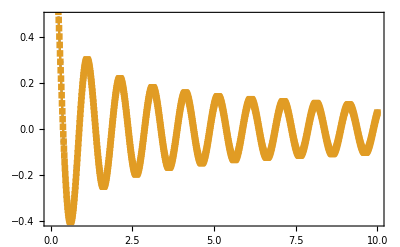

```mathematica
ListPlot[{Table[{ii,f[2π,ii,.1]},{ii,0,10,.1}],Table[{ii,BesselJ[0,N[2π]ii]},{ii,0,10,.01}]}]
```

```mathematica
Integrate[1,{px,0,Λ},{py,0,Λ}]
```

Λ^2

```mathematica
Integrate[(q BesselJ[0,q*x])/(q^2+Λ),{q,0,∞}]
```

$Aborted

```mathematica
Series[1/Sqrt[(1/(uu kk)+(gamma gg^2 kk beta^4 π)/(8 uu^2)dl)*(uu/kk+(gamma gg^2 kk beta^4 π)/8 dl)],{dl,0,1}]//FullSimplify
```

```mathematica
(1/(√(1/kk^2))-((beta^4 gamma gg^2 π) dl)/(8 ((1/kk^2)^(3/2) uu)))/(1/(√(1/kk^2)))//FullSimplify
```

```mathematica
(√(1/kk^2)+(beta^4 gamma gg^2 π dl)/(8 √(1/kk^2) uu))/√(1/kk^2)//FullSimplify
```

```mathematica
Clear[dk,dg]
dk[g_,γ_,u_,κ_]:=-(π*g^2*γ*κ^3)/(8 u)
dg[κ_,g_]:=(2-κ/4)g
```

```mathematica
Manipulate[VectorPlot[{-dg[kk,gg],dk[gg,gamma,uu,kk]},{gg,-1,1},{kk,0,1}],{beta,0,1},{gamma,1,10},{uu,1,10}]
```

```mathematica
tt[beta_,kk_]:=(beta^2 kk)/4-2
yy[gamma_,gg_,uu_]:=√((π gamma)/uu) 4 gg
```

```mathematica
points=Tuples[{-3,-2,-1,0,1,2,3,4,5,6}*.5,2]+.005
```

{{-1.495,-1.495},{-1.495,-0.995},{-1.495,-0.495},{-1.495,0.005},{-1.495,0.505},{-1.495,1.005},{-1.495,1.505},{-1.495,2.005},{-1.495,2.505},{-1.495,3.005},{-0.995,-1.495},{-0.995,-0.995},{-0.995,-0.495},{-0.995,0.005},{-0.995,0.505},{-0.995,1.005},{-0.995,1.505},{-0.995,2.005},{-0.995,2.505},{-0.995,3.005},{-0.495,-1.495},{-0.495,-0.995},{-0.495,-0.495},{-0.495,0.005},{-0.495,0.505},{-0.495,1.005},{-0.495,1.505},{-0.495,2.005},{-0.495,2.505},{-0.495,3.005},{0.005,-1.495},{0.005,-0.995},{0.005,-0.495},{0.005,0.005},{0.005,0.505},{0.005,1.005},{0.005,1.505},{0.005,2.005},{0.005,2.505},{0.005,3.005},{0.505,-1.495},{0.505,-0.995},{0.505,-0.495},{0.505,0.005},{0.505,0.505},{0.505,1.005},{0.505,1.505},{0.505,2.005},{0.505,2.505},{0.505,3.005},{1.005,-1.495},{1.005,-0.995},{1.005,-0.495},{1.005,0.005},{1.005,0.505},{1.005,1.005},{1.005,1.505},{1.005,2.005},{1.005,2.505},{1.005,3.005},{1.505,-1.495},{1.505,-0.995},{1.505,-0.495},{1.505,0.005},{1.505,0.505},{1.505,1.005},{1.505,1.505},{1.505,2.005},{1.505,2.505},{1.505,3.005},{2.005,-1.495},{2.005,-0.995},{2.005,-0.495},{2.005,0.005},{2.005,0.505},{2.005,1.005},{2.005,1.505},{2.005,2.005},{2.005,2.505},{2.005,3.005},{2.505,-1.495},{2.505,-0.995},{2.505,-0.495},{2.505,0.005},{2.505,0.505},{2.505,1.005},{2.505,1.505},{2.505,2.005},{2.505,2.505},{2.505,3.005},{3.005,-1.495},{3.005,-0.995},{3.005,-0.495},{3.005,0.005},{3.005,0.505},{3.005,1.005},{3.005,1.505},{3.005,2.005},{3.005,2.505},{3.005,3.005}}

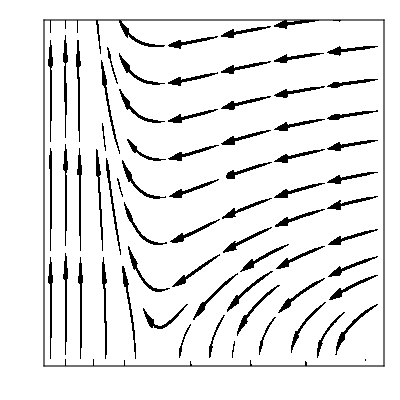

```mathematica
ticks={{Join[Table[{i,If[i<3,MaTeX[NumberForm[i,{4,1}]],""],ts},{i,0,4,.5}],Table[{i,"",0.5ts},{i,.25,4,.5}],{{2.9,Rotate[MaTeX["y"],0],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<4,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,-4,4,1}],Table[{i,"",0.5ts},{i,-4.5,4,1}],{{3.75,MaTeX["x"],.0}}],{None}}}; 
p1=StreamPlot[{-y^2/16 2*(t+2)^3,-t y},{t,(tmin=-4),(tmax=4)},{y,(ymin=-4),(ymax=4)},StreamPoints->100,StreamMarkers->"PinDart",StreamScale->0.11,StreamStyle->Black,PlotRangePadding->0,PlotRange->{{-2,tmax},{0,3}},FrameStyle->Black,FrameTicks->ticks,ImageSize->{Automatic,156},AspectRatio->1,GridLines->None,PlotRangePadding->0,ImagePadding->{{25,2},{20,2}}]
```

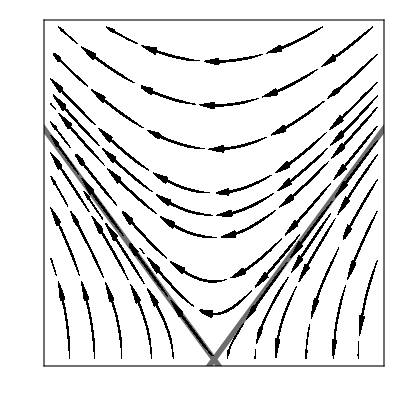

```mathematica
ticks={{Join[Table[{i,If[i<2*10^-2,MaTeX[NumberForm[i*10^2,{4,1}]],""],ts},{i,0,4*10^-2,.5*10^-2}],Table[{i,"",0.5ts},{i,.25*10^-2,4*10^-2,.5*10^-2}],{{2.5*10^-2,Rotate[MaTeX["y[\\times 10^{-2}]"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<1*10^-2,MaTeX[NumberForm[i*10^2,{4,2}]],""],ts},{i,-4*10^-2,4*10^-2,1*10^-2}],Table[{i,"",0.5ts},{i,-4.5*10^-2,4*10^-2,1*10^-2}],{{1.4*10^-2,MaTeX["x[\\times 10^{-2}]"],.0}}],{None}}}; 
p2=Show[StreamPlot[{-y^2/16 2*(t+2)^3,-t y},{t,(tmin=-2*10^-2),(tmax=2*10^-2)},{y,(ymin=0),(ymax=3*10^-2)},StreamPoints->20,StreamMarkers->"PinDart" ,StreamScale->.175,StreamStyle->Black,PlotRangePadding->0,PlotRange->{{tmin,tmax},{ymin,ymax}},FrameStyle->Black,FrameTicks->ticks,ImageSize->{Automatic,156},AspectRatio->1,FrameTicks->ticks,GridLines->None,PlotRangePadding->0,ImagePadding->{{25,2},{20,2}}],ListPlot[{{-1,-1},{1,1}},PlotStyle->{Thickness[.01],mygray}],ListPlot[{{1,-1},{-1,1}},PlotStyle->{Thickness[.01],mygray}],StreamPlot[{-y^2/16 2*(t+2)^3,-t y},{t,(tmin=-2*10^-2),(tmax=2*10^-2)},{y,(ymin=0),(ymax=3*10^-2)},StreamPoints->20,StreamMarkers->"PinDart" ,StreamScale->.175,StreamStyle->Black,PlotRangePadding->0,PlotRange->{{tmin,tmax},{ymin,ymax}},FrameStyle->Black,FrameTicks->ticks,ImageSize->{Automatic,156},AspectRatio->1,FrameTicks->ticks,GridLines->None,PlotRangePadding->0,ImagePadding->{{25,2},{20,2}}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export["BKT_RG_flow1.png",p1,ImageResolution->1200]
Export["BKT_RG_flow2.png",p2,ImageResolution->1200]
```

{2,4,6,8}

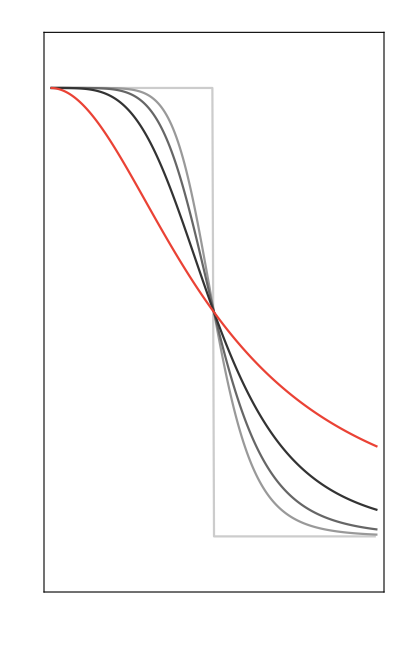

{110,156}

```mathematica
chis={2,4,6,8}
(*chis={2}*)
pts=ts;
ts=244/110*ts;
ticks={{Join[Table[{i,If[i<.8,MaTeX[NumberForm[Round[10*i]/10//N,{4,1}]],""],ts},{i,-1.,2,.5}],Table[{i,"",0.5ts},{i,-1.25,4,.5}],{{0.9,Rotate[MaTeX["f_n(p,\\Lambda)"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<2,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,-4,4,1}],Table[{i,"",0.5ts},{i,-4.5,4,1}],{{1.85,MaTeX["p/\\Lambda"],.0}}],{None}}}; 
ts=pts; 
p4=ListPlot[Evaluate[Join[{Table[{x,HeavisideTheta[1-x]},{x,0.0001,2,0.01}]},Table[{x,(2π)^χ/((x*2π)^χ+(2π)^χ)},{χ,Reverse[chis]},{x,0,2,0.01}]]],Joined->True,PlotMarkers->False,PlotStyle->Table[Directive[If[ii==Length[chis]+1,myred,Blend[{Black,White},1-ii/(Length[chis]+1)]]],{ii,Length[chis]+1}],ImageSize->{Automatic,156},AspectRatio->GoldenRatio,FrameTicks->ticks,ImagePadding->{{25,2},{20,2}},PlotRangePadding->0,PlotRange->{{0,2},{-.1,1.1}}]
ImageDimensions[p4]
```

```mathematica
Clear[fchi,cchi,χ]
Monitor[
Do[
fchi[χ][x_,Λ_]=Integrate[BesselJ[0,p x]  p^(χ-1)/(p^χ+Λ^χ),{p,0,∞},Assumptions->Λ>0&&x>0];
cchi[χ][x_,Λ_]=Normal[Series[fchi[χ][x,Λ-dΛ]-fchi[χ][x,Λ],{dΛ,0,1}]]/.{dΛ->1};
,{χ,chis}],χ]
```

Do::iterb: Iterator {χ,chis} does not have appropriate bounds.

Do[fchi[χ][x_,Λ_]=Integrate[(BesselJ[0,p x] p^(χ-1))/(p^χ+Λ^χ),{p,0,∞},Assumptions→Λ>0&&x>0];cchi[χ][x_,Λ_]=Normal[Series[fchi[χ][x,Λ-dΛ]-fchi[χ][x,Λ],{dΛ,0,1}]]/.{dΛ→1};,{χ,chis}]

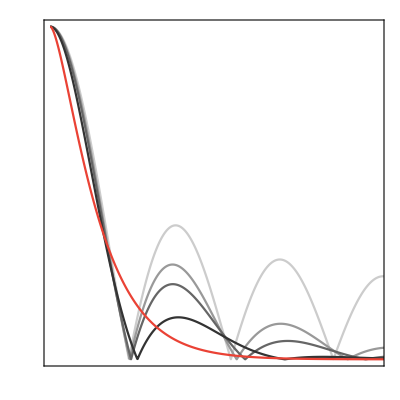

{161,156}

```mathematica
pts=ts;
ts=244/110*ts;
ticks={{Join[Table[{i,If[i<.8,MaTeX[NumberForm[Round[10*i]/10//N,{4,1}]],""],ts},{i,-1.,2,.5}],Table[{i,"",0.5ts},{i,-1.25,4,.5}],{{0.85,Rotate[MaTeX["|C(r)|"],π/2],0*ts}}],Join[{},{{1,(*MaTeX["D_\\parallel+D_\\perp"]*)"",{0.,0}}}]},{Join[Table[{i,If[i<7,MaTeX[NumberForm[i,{4,2}]],""],ts},{i,-4,10,2}],Table[{i,"",0.5ts},{i,-3,10,2}],{{9,MaTeX["\\Lambda r"],.0}}],{None}}}; 
ts=pts; 
p3=ListPlot[Join[{Table[{ x,Abs[BesselJ[0,x]]},{x,0.001,20,.01}]},Table[Table[{x,Abs[cchi[χ][x,1]]},{x,0.0001,20,.01}],{χ,Reverse[chis]}]],PlotMarkers->None,PlotRange->{{0.01,10},{10^-12,1.}},PlotStyle->(colors=Table[Directive[If[ii==Length[chis]+1,myred,Blend[{Black,White},1-ii/(Length[chis]+1)]]],{ii,Length[chis]+1}]),ImageSize->{Automatic,156},AspectRatio->1,FrameTicks->ticks,ImagePadding->{{25,2},{20,2}}]
ImageDimensions[p3]
```

```mathematica
colors[[{5,1}]]
```

{Directive[RGBColor[0.9176470588, 0.2588235294, 0.2078431373]],Directive[GrayLevel[Rational[4, 5]]]}

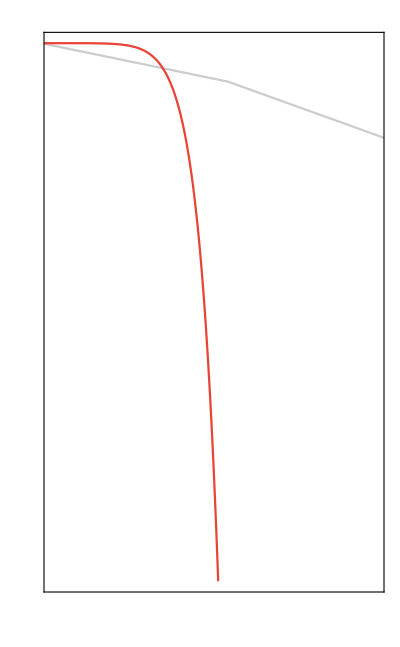

{110,156}

```mathematica
pts=ts;
ts=244/110*ts;
ticks={{Join[Table[{10^-i,If[i>3,Rotate[MaTeX["10^{-"<>ToString[IntegerPart[Round[i]//N]]<>"}"],π/2],""],ts},{i,2.,18,4}],Table[{10^-i,"",0.5ts},{i,4,18,4}],{{10^-2,Rotate[MaTeX["|C(r)|"],π/2],0*ts}}],{}},{Join[Table[{10^i,If[i<4,MaTeX["10^{"<>ToString[IntegerPart[i]]<>"}"],""],ts},{i,-1,5,2}],Table[{10^i,"",0.5ts},{i,-2,5,2}],{{10^4*4,MaTeX["\\Lambda r"],.0}}],{}}}; 
ts=pts; 
p5=Show[ListLogLogPlot[{Table[{2π x,Abs[BesselJ[0,2π x]]},{x,0.001,10^5,10}],Table[{2π x,Abs[cchi[2][x,N[2π]]]2π},{x,0.0001,20,.01}]},PlotMarkers->None,PlotRange->{{0.01,10^5},{10^-16,1.}},PlotStyle->colors[[{1,5}]],ImageSize->{Automatic,156},AspectRatio->GoldenRatio,ImagePadding->{{25,2},{20,2}},FrameTicks->ticks]]
ImageDimensions[p5]
```

```mathematica
42/(2π)//N
```

6.68451

```mathematica
6.684507609859605
```

```mathematica
Λ*cchi[2][x,Λ]/.{Λ->2π}/.{x->12.4π/(2π)}//N
```

9.53251×10^-17

```mathematica
x BesselK[1,x]/.{x->2π}//N
```

0.00620148

```mathematica
Abs[cchi[2][1,N[2π]]]2π
```

0.00620148

```mathematica
cchi[2][x,Λ]
```

x BesselK[1,x Λ]

```mathematica
Limit[BesselJ[0,Λ x],x->0]
```

1

```mathematica
Limit[cchi[2][x,Λ],x->0]
```

1/Λ

```mathematica
Integrate[cchi[2][x,Λ],{x,a,∞},Assumptions->a>0&&Λ>0]
```

Integrate[x BesselK[1,x Λ],{x,a,∞},Assumptions→a>0&&Λ>0]

```mathematica
2^(-2-1)Csc[Pi 1]
```

ComplexInfinity

```mathematica
Limit[(2^(-2-ν) Pi z Csc[Pi ν] (4^ν Sqrt[Pi] HypergeometricPFQRegularized[{1/2},{1-ν,3/2},z^2/4]-z^(2 ν) Gamma[1/2+ν] HypergeometricPFQRegularized[{1/2+ν},{1+ν,3/2+ν},z^2/4]))/.{z->10},ν->1]
```

ConditionalExpression[5/6 (75 √π HypergeometricPFQRegularized^({0},{0,1},0)[{3/2},{2,5/2},25]+6 √π HypergeometricPFQRegularized^({0},{1,0},0)[{1/2},{0,3/2},25]+25 (4 HypergeometricPFQ[{3/2},{2,5/2},25] (Log[25]+PolyGamma[0,3/2])+3 √π HypergeometricPFQRegularized^({0},{1,0},0)[{3/2},{2,5/2},25]+3 √π HypergeometricPFQRegularized^({1},{0,0},0)[{3/2},{2,5/2},25])),(-HypergeometricPFQRegularized^({0},{0,1},0)[{3/2},{2,5/2},25]-HypergeometricPFQRegularized^({0},{1,0},0)[{3/2},{2,5/2},25]-HypergeometricPFQRegularized^({1},{0,0},0)[{3/2},{2,5/2},25]|HypergeometricPFQRegularized^({0},{0,1},0)[{3/2},{2,5/2},25]+HypergeometricPFQRegularized^({0},{1,0},0)[{3/2},{2,5/2},25]+HypergeometricPFQRegularized^({1},{0,0},0)[{3/2},{2,5/2},25]|HypergeometricPFQRegularized^({0},{1,0},0)[{1/2},{0,3/2},25]|HypergeometricPFQRegularized^({0},{2,0},0)[{1/2},{0,3/2},25]|HypergeometricPFQRegularized^({0},{0,2},0)[{3/2},{2,5/2},25]+2 HypergeometricPFQRegularized^({0},{1,1},0)[{3/2},{2,5/2},25]+HypergeometricPFQRegularized^({0},{2,0},0)[{3/2},{2,5/2},25]+2 HypergeometricPFQRegularized^({1},{0,1},0)[{3/2},{2,5/2},25]+2 HypergeometricPFQRegularized^({1},{1,0},0)[{3/2},{2,5/2},25]+HypergeometricPFQRegularized^({2},{0,0},0)[{3/2},{2,5/2},25])∈ℝ]

```mathematica
ImageDimensions[p3]
```

{161,156}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreas/Dropbox

```mathematica
Export["cutoff_function.png",p4,ImageResolution->1200]
```

cutoff_function.png

```mathematica
Export["rg_correlations.png",p3,ImageResolution->1200]
```

rg_correlations.png

```mathematica
Export["rg_correlations_log.png",p5,ImageResolution->1200]
```

rg_correlations_log.png

```mathematica
ImageDimensions[p4]
```

{161,156}

```mathematica
BesselJ[0,Λ*x]
```

```mathematica
Integrate[BesselJ[0,p x]  (p^(χ-1)/(p^χ+Λ^χ)-p^(χ-1)/(p^χ+Λpr^χ))/.{χ->2},{p,0,∞},Assumptions->Λ>0&&Λpr>0&&x>0]
```

BesselK[0,x Λ]-BesselK[0,x Λpr]

```mathematica
Integrate[BesselJ[0,p x]  (p^(-1+χ) Λ^(-1+χ) χ)/((p^χ+Λ^χ)^2)/.{χ->2},{p,0,∞},Assumptions->Λ>0&&x>0]
```

x BesselK[1,x Λ]

```mathematica
fchi[2][x,Λ]
```

BesselK[0,x Λ]

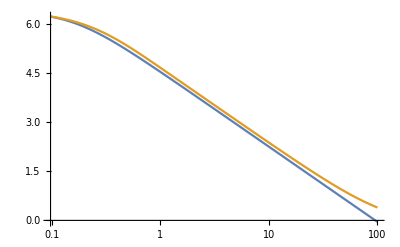

```mathematica
L=600;
lmin=2π/L;
lmax=2π;
LogLinearPlot[Evaluate[{- 1/2 Log[(r^2+(lmax)^-2)/(lmin)^-2],(BesselK[0,lmin*r]-BesselK[0,lmax*r])}],{r,0,100},PlotRange->Full]
```

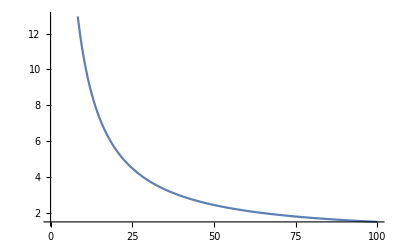

```mathematica
Plot[Exp[BesselK[0,lmin*r]],{r,0,100}]
```

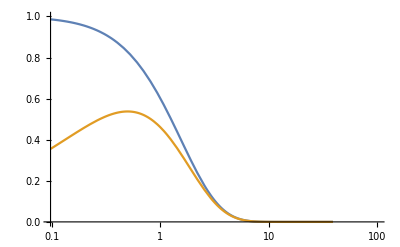

```mathematica
LogLinearPlot[{x BesselK[1,x],√(x π/2)ⅇ^-x},{x,0,100},PlotRange->{10^-16,1}]
```

```mathematica
Integrate[√(x π/2)ⅇ^-x,{x,0,∞}]
```

π/(2 √2)

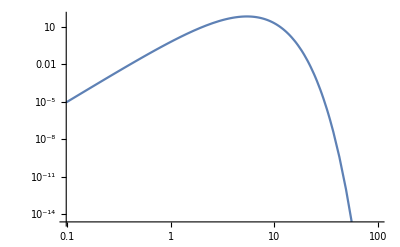

```mathematica
LogLogPlot[Abs[x^6 BesselK[1,x]],{x,0,100}]
```

```mathematica
{{"-0.6012","0.5399"}}
```

```mathematica
{{"-0.5575","0.5831"}}
```

```mathematica
{{"-0.5942","0.549"}}
```

```mathematica
{{"-0.5834","0.5618"}}
```

```mathematica
(ToExpression[{{"-0.5915","0.5519"}}]+ToExpression[{{"-0.5884","0.5549"}}])/2
```

{{-0.58995,0.5534}}

```mathematica
p=-0.5897+0.5535 I
```

-0.5897+0.5535 ⅈ

```mathematica
img=Table[ImageData[ImageEffect[MandelbrotSetPlot[p+0.0015*{(-1*110/156+-I),(1*110/156+I)},MaxIterations->200,EscapeRadius->100,ImageResolution->1200,Frame->None,PlotRangePadding->None],{"Noise",tt}]],{tt,nl={0,0.05,0.1,0.2,0.4,0.8}}];
```

```mathematica
tp=ArrayReshape[RandomReal[1,{1200,1200}],{1200,1200}];
tp=tp-IdentityMatrix[1200]*Tr[tp]/1200;
tp = tp/√Tr[tp^2];
{u,l,v}=SingularValueDecomposition[tp];
```

```mathematica
Clear[lls,imgpr]
lls={};
imgpr={};
Do[
{d1,d2,d3}=Dimensions[ii];
tp=ArrayReshape[ii,{d1,d2*d3}];
{u,l,v}=SingularValueDecomposition[tp];
norm=Norm[Diagonal[l]];

tr=100;
norm2=Norm[Diagonal[l][[;;tr]]];
tppr=ArrayReshape[u[[;;,;;tr]].l[[;;tr,;;tr]].(v†[[;;tr,;;]])/norm2*norm,{d1,d2,d3}];
tppr=ArrayReshape[u[[;;,;;tr]].l[[;;tr,;;tr]].(v†[[;;tr,;;]]),{d1,d2,d3}];
tpimg=Show[Image[tppr],ImagePadding->{{25,2},{20,2}},ImageSize->{Automatic,156}];


AppendTo[lls,Diagonal[l]];
AppendTo[imgpr,tpimg];
,{ii,img}];
```

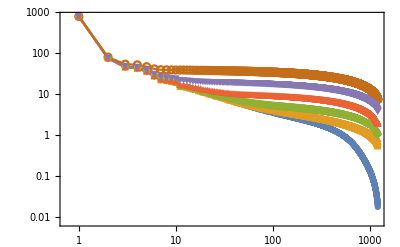

```mathematica
ListLogLogPlot[lls]
```

```mathematica
pts=ts;
ts=244/110*ts;
ticks={{Join[Table[{10^i,If[i<3,Rotate[MaTeX["10^{"<>ToString[IntegerPart[Round[i]//N]]<>"}"],π/2],""],ts},{i,-1,4,1}],Table[{10^-i,"",0.5ts},{i,4,18,4}],{{0.6*10^3,Rotate[MaTeX["S_k"],π/2],0*ts}}],{}},{Join[Table[{10^i,If[i<3,MaTeX["10^{"<>ToString[IntegerPart[i]]<>"}"],""],ts},{i,-1,5,1}],{{10^3,MaTeX["k"],.0}}],{}}}; 
ts=pts;
```

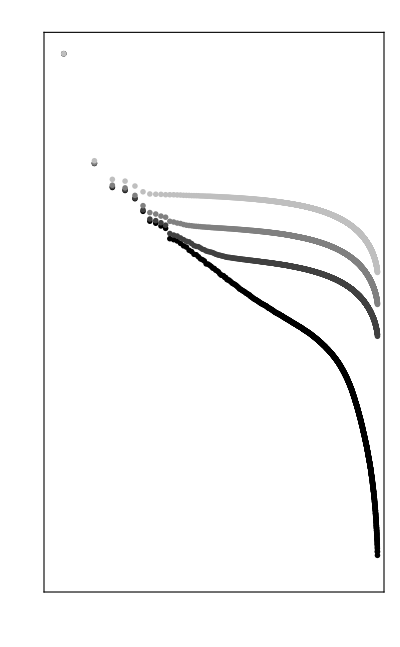

```mathematica
sel={1,4,5,6};
svplot=ListLogLogPlot[lls[[sel]],PlotRange->{Automatic,{10^-2,10^3}},Joined->False,PlotMarkers->{"●",Scaled[.05]},FrameTicks->ticks,AspectRatio->GoldenRatio,ImagePadding->{{25,2},{20,2}},ImageSize->{Automatic,156},PlotStyle->Table[Blend[{Black,White},ii],{ii,0,1,1/Length[sel]}],GridLines->{{{100,Directive[Black,Opacity[1]]}},{}}]
```

```mathematica
tickso=Table[{{Join[{},{},{{0.6*10^3,Rotate[MaTeX["\\text{original, noise level}\\equiv"<>ToString[nn]],π/2],0*ts}}],{}},{Join[{},{}],{}}} ,{nn,nl}];
ticksa=Table[{{Join[{},{},{{0.575*10^3,Rotate[MaTeX["\\text{approximation, noise level}\\equiv"<>ToString[nn]],π/2],0*ts}}],{}},{Join[{},{}],{}}} ,{nn,nl}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
Table[Export["mandelbrot_noise_original"<>ToString[ii]<>".png",Show[Image[img[[ii]]],AspectRatio->GoldenRatio,ImagePadding->{{25,2},{20,2}},ImageSize->{Automatic,156},Frame->True,FrameStyle->White,FrameTicks->tickso[[ii]]],ImageResolution->1200],{ii,Length[img]}]
```

/Users/Andy/Dropbox

{mandelbrot_noise_original1.png,mandelbrot_noise_original2.png,mandelbrot_noise_original3.png,mandelbrot_noise_original4.png,mandelbrot_noise_original5.png,mandelbrot_noise_original6.png}

```mathematica
SetDirectory[NotebookDirectory[]]
Table[Export["mandelbrot_noise_approx"<>ToString[ii]<>".png",Show[Image[imgpr[[ii]]],AspectRatio->GoldenRatio,ImagePadding->{{25,2},{20,2}},ImageSize->{Automatic,156},Frame->True,FrameStyle->White,FrameTicks->ticksa[[ii]]],ImageResolution->1200],{ii,Length[imgpr]}]
```

/Users/Andy/Dropbox

{mandelbrot_noise_approx1.png,mandelbrot_noise_approx2.png,mandelbrot_noise_approx3.png,mandelbrot_noise_approx4.png,mandelbrot_noise_approx5.png,mandelbrot_noise_approx6.png}

```mathematica
SetDirectory[NotebookDirectory[]]
Export["mandelbrot_svds.png",svplot,ImageResolution->600]
```

/Users/Andy/Dropbox

mandelbrot_svds.png